```mathematica
prob =Sin[ Ω t/2]^2
```

Sin[(t Ω)/2]^2

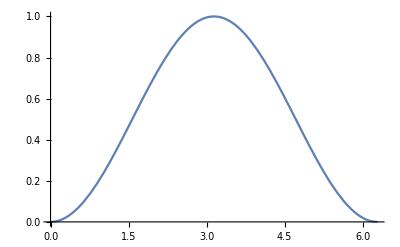

```mathematica
Plot[prob/.Ω->1, {t, 0, 2π}]
```

```mathematica
timespent=Integrate[prob, {t, 0, π}]*1/Ω
```

(π-Sin[π Ω]/Ω)/(2 Ω)

```mathematica
timespent/.\
```

```mathematica
(70/50)^17//N
```

304.913